1.033

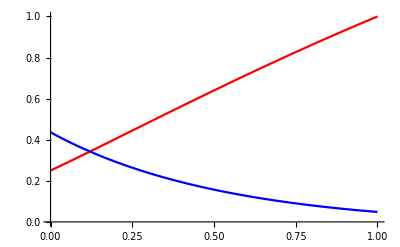

-Graphics3D-

```mathematica
fpi=0.132;
feta=fpi*1.26;
mupi=2.64;
mueta=2.32;
k=1.033

pi0p[x_]:=fpi*mupi/Sqrt[2](2+x);
pi0n[x_]:=fpi*mupi/Sqrt[2](1+2x);
etap[x_,n_]:=feta*mueta*k*n/Sqrt[6.]*(2-x);
Plot[{(pi0n[x]/pi0p[x])^2,(etap[x,1.]/pi0p[x])^2},{x,0,1},PlotStyle->{Red,Blue}]

Plot3D[{(pi0n[x]/pi0p[x])^2,(etap[x,n]/pi0p[x])^2},{x,0,1},{n,1,2},PlotStyle->{Red,Blue}]
```